```mathematica
(*Тут генерация точек, и так сойдет. И для двумерных пока*)
SeedRandom[42];
R=2;(*расмерность пространства*)
coefNonZero="1100011";(*начальные состояния атомов  "110000110000" *)
n=StringLength[coefNonZero]; (*количество атомов*)
points=RandomVariate[NormalDistribution[0,R],{n,2}];(*координаты атомов*)
distAr=ConstantArray[0,{n,n}]; (*массив расстояний между точками/атомами*)
Do[Do[
distAr[[i]][[j]]=EuclideanDistance[points[[i]],points[[j]]]
,{j,1,n}],{i,1,n}]
distAr;
```

```mathematica
(*тут создание матриц, перепутывающих 2 каких-то атома с номерами (i1, i2) в системе из size атомов*)
Createf[size_,i1_,i2_]:=
Module[{num,tmp,copynum},
f=ConstantArray[0,{2^size,2^size}];
If[i1>n ||i2>n||i1==i2,Print["Ты облажался с индексами"];Return[];];
Do[
num =IntegerDigits[i,2,size];
copynum=num;
tmp=num[[i1]];
num[[i1]]=num[[i2]];
num[[i2]]=tmp;
f[[FromDigits[copynum,2]+1,FromDigits[num,2]+1]]= 1
,{i,0,2^size-1}];
Return[f]
]
```

```mathematica
(*Кусок кода, который находит среднее значение матриц плотности, перебирая всевозможные группы размера size.*)
(*size=n; количество элементов в рассматриваемых группах атомов*)
Clear[t];
GetNum[num_]:=ToExpression[StringPart[coefNonZero,num]];(*функция, которая возвращает нужное число в десятичной системе*)
GetSol[size_]:=Module[{allGroups ,T,Tn,h,rhoSize,sol,idxArray,e,v0,w,listOfAllPairIdx,t},
allGroups =Subsets[Range[1,n],{size}]; (*всевозможные группы размера size*)
T=4 Pi;
Tn=100;
h=T/(Tn+1);
rhoSize={}; (*тут будут хранится полученные матрицы плотности для всевозможных групп*)
sol={};
avgRhoSize={};
tarray={};

Do[
t=(idxt-1) h;
AppendTo[tarray,t];
Do[
idxArray=allGroups[[idxGroup]]; (*индексы в исходной нумерации атомов*)
e=IdentityMatrix[2^size]; (*единичная матрица*)
v0=ConstantArray[0,2^size]; (*вектор начальных условий, единичка добавляется потом*)

v0[[FromDigits[Table[GetNum[idxArray[[idx]]],{idx,1,size}],2]+1]]=1 ;(*вектор начальных условий*)
listOfAllPairIdx=Subsets[Range[1,size],{2}];(*список всех не повторяющихся элементов по 2 индекса, для генерачии матриц f_{i1,i2}*)
w=Total[Table[
1/distAr[[idxArray[[listOfAllPairIdx[[idxPair,1]]]],idxArray[[listOfAllPairIdx[[idxPair,2]]]]]]  (Createf[size,listOfAllPairIdx[[idxPair,1]],listOfAllPairIdx[[idxPair,2]]]),{idxPair,Length[listOfAllPairIdx]}]];
(*sol=DSolveValue[{I v'[t]==w.v[t],
v[0]==v0}, Element[v[t],Vectors[2^size]],t];*)
sol=N[MatrixExp[-I w t,v0]];
AppendTo[rhoSize, TensorProduct[sol,Transpose[Conjugate[sol]]]];
,{idxGroup,1, Length[allGroups]}];
AppendTo[avgRhoSize, Total[rhoSize]/Length[rhoSize]],
{idxt,1,Tn+2}];
{tarray,avgRhoSize}
]
```

```mathematica
(*тут типа средниме матрицы во времени*)
GetRedused[sol_,size_,part_]:=Module[{list1},
list1=Subsets[Range[1,size],{size-part}];
Table[  Total[Table[ResourceFunction["MatrixPartialTrace"][sol[[idxt]],list1[[idxL]],2],{idxL, 1, Length[list1]}]]/Length[list1],{idxt,1,Length[avgRhoSize]}]
]
```

```mathematica
PlotDiag[tsol_,redused_,part_]:=Module[{data},
data={};
Do[
AppendTo[data,Table[{tsol[[1,id]],redused[[id,j,j]]},{id,1,Length[tarray]}]];
,{j,1,2^part}];
ListPlot[data,PlotRange->All,Joined->True,PlotLegends->Automatic,PlotLabel->"Диагональные элементы"]
]
```

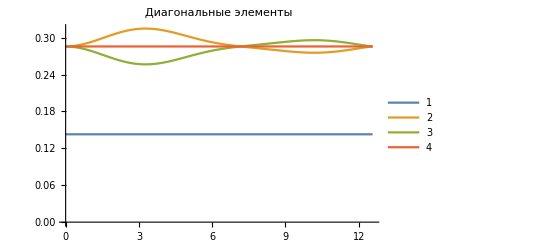

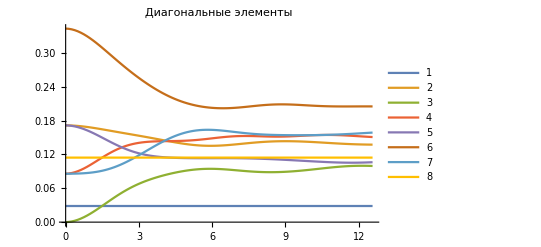

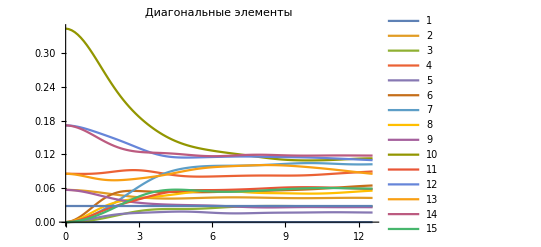

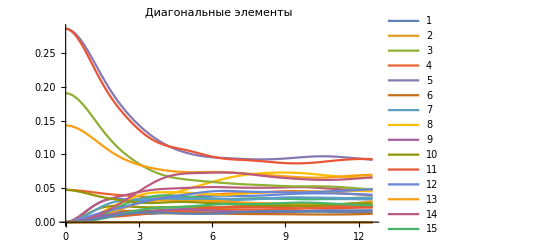

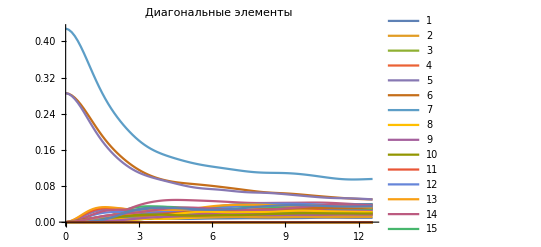

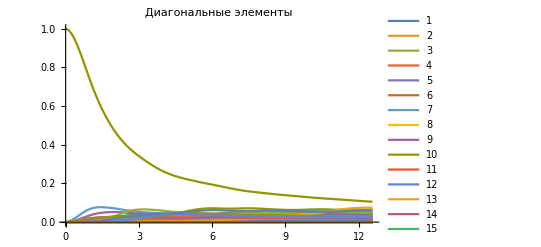

```mathematica
(*тут усредненные матрицы всевозможных групп атомов*)
size=3; (*размер группы атомов для которой решаем*)
Do[
tsol21=GetSol[size];(*среднее решение для групп атомов определённого размера*)
part=size;(*2^part-количество диагональных элементов*)
Print[PlotDiag[tsol21,tsol21[[2]],part]]
,{size,2,n}]
```

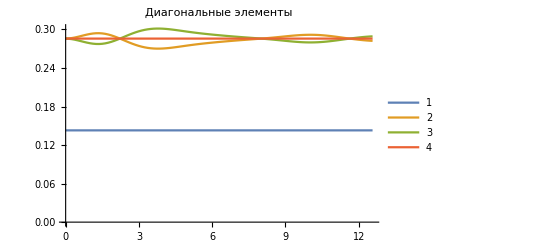

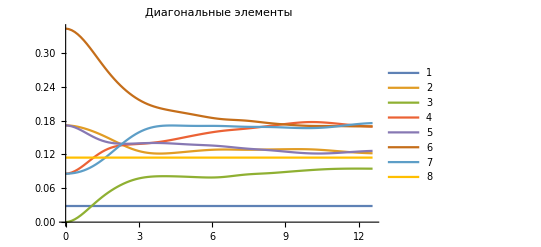

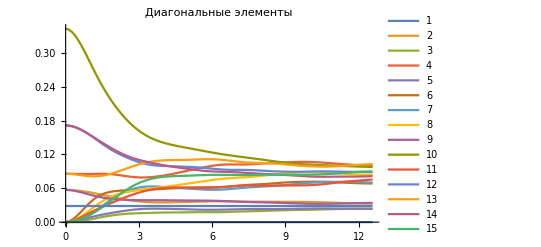

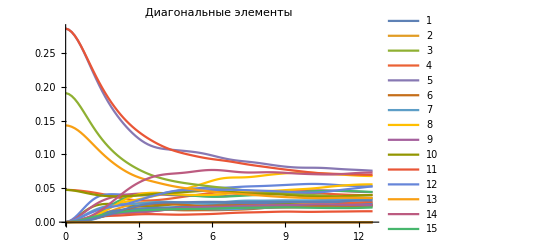

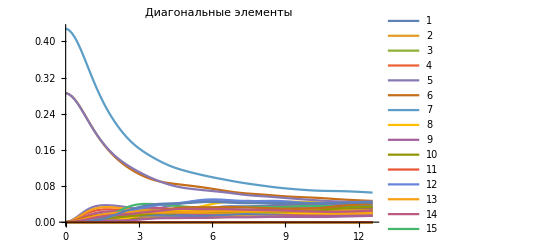

-Graphics-

```mathematica
(*диагональные элементы редуцированных матриц плотности*)
size=n; (*размер группы атомов для которой решаем*)
tsol21=GetSol[size];(*среднее решение для групп атомов определённого размера*)
Do[
avgRDM4t=GetRedused[tsol21[[2]],size, part];
Print[PlotDiag[tsol21,avgRDM4t,part]]
,{part,2,n}]
```